## Discrete Fourier Transform (Test)

Implement function for transforming degrees to radians

```mathematica
rad[deg_]:=deg*π/180;
deg[rad_]:=rad*180/π;
```

### Create mapper function

The mapper function takes a pure function f that depends on one argument and applies it to an entire list of sampled-data points (N-data points)

```mathematica
mapper[function_,data_]:=Map[function,data];
export[path_,object_]:=Export[StringTemplate["````.pdf"][NotebookDirectory[],path],object,ImageSize->Large];
```

### Generate a sampled data with fixed size

```mathematica
xdataRaw[N_]:=Table[deg,{deg,60/N,60,60/N}];
xdata[N_]:=mapper[rad,xdataRaw[N]];
```

## Generate the function data points from the function method itself

### the function “f2” has an additional phase shift as compared to “f1”

### test function “f”

```mathematica
(*declare a constant phase to be used within calculations*)
phase=45;
f1[x_]:=2Sin[x]+Sin[3x];
f2[x_]:=2Sin[x+rad[phase]]+Sin[3x];
mydata=xdata[30];
```

## Create plot data from the given function values

```mathematica
f1ydata[data_]:=N[mapper[f1,data]];
f2ydata[data_]:=N[mapper[f2,data]];
```

## Create graphical representation with the function values

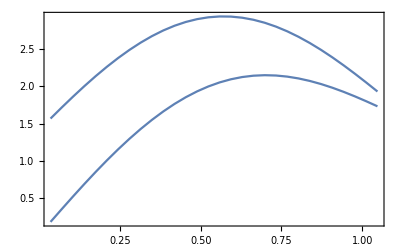

```mathematica
plotter[xdata_,ydata_]:=ListPlot[Table[{xdata[[i]],ydata[[i]]},{i,1,Length[xdata]}],Joined->True,Frame->True,Axes->False];
Show[plotter[mydata,f1ydata[mydata]],plotter[mydata,f2ydata[mydata]],PlotRange->Full]
```